# ListDensityPlot de 1/100∫_0^100 𝔼[Tr[𝒟^2(t)] ]dt

```mathematica
SetDirectory[NotebookDirectory[]];
```

## XXZ with defect

## XXZ L=7,d=4,J_z=1,ω=0, barriendo ε y J_xy de 0 a 2 (paso = 0.1)

```mathematica
(* Datos del promedio temporal del valor esperado de Haar de la pureza de Choi *)
{#[[1]],choiPurity=#[[2;;]];}&[Import["data/temporal_haar_avg_choi_purity/xxz_w_defect_L_7_Jz_1_d_4_omega_0.csv"]]
```

{{\varepsilon,J_{xy},promedio temporal de 0 a 100 del valor esperado de Haar de la pureza de Choi},Null}

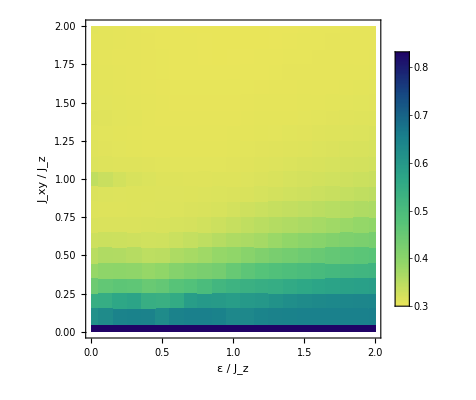

```mathematica
fontSize=22;

fig=ListDensityPlot[choiPurity,
ColorFunction->(ColorData["BlueGreenYellow"][1-#]&),ColorFunctionScaling->True,
PlotRange->{Min[#],Max[#]}&[choiPurity[[All,3]]],
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"ε / J_z","J_xy / J_z"}
]
```

```mathematica
filename="figs_ja/temporal_avg_haar_avg_choi_purity_xxz_L_7_Jz_1_omega_0_d_4.pdf";
Export[filename,fig,"PDF",ImageResolution->300]
```

figs_ja/temporal_avg_haar_avg_choi_purity_xxz_L_7_Jz_1_omega_0_d_4.pdf

```mathematica
RunProcess[{"pdfcrop",filename,filename}]
```

<|ExitCode→0,StandardOutput→PDFCROP 1.42, 2023/04/15 - Copyright (c) 2002-2023 by Heiko Oberdiek, Oberdiek Package Support Group.
==> 1 page written on `figs_ja/temporal_avg_haar_avg_choi_purity_xxz_L_7_Jz_1_omega_0_d_4.pdf'.
,StandardError→|>

## XXZ L=7,d=3,J_z=1,ω=0, barriendo ε y J_xy de 0 a 2 (paso = 0.1)

```mathematica
(* Datos del promedio temporal del valor esperado de Haar de la pureza de Choi *)
{#[[1]],choiPurity=#[[2;;]];}&[Import["data/temporal_haar_avg_choi_purity/xxz_w_defect_L_7_Jz_1._d_3_omega_0..csv"]]
```

{{\varepsilon,J_{xy},promedio temporal de 0 a 100 del valor esperado de Haar de la pureza de Choi},Null}

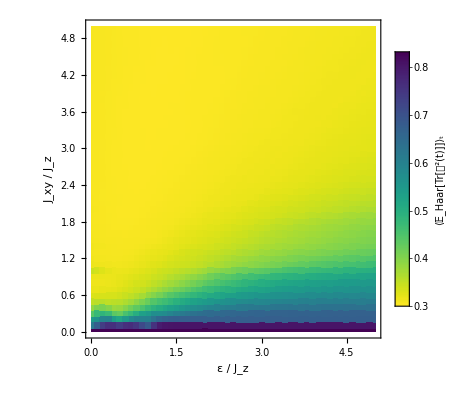

```mathematica
fontSize=22;
fig=ListDensityPlot[choiPurity,
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->{Min[choiPurity[[All,3]]],Max[Select[choiPurity[[All,3]],#<1.&]]},
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->Style["⟨𝔼_Haar[Tr[𝒟^2(t)]]⟩_t",16],LabelStyle->Directive[FontFamily->"Arial",FontSize->18,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"ε / J_z","J_xy / J_z"}
]
```

```mathematica
filename="figs_ja/temporal_avg_haar_avg_choi_purity/xxz_L_7_Jz_1_omega_0_d_3.pdf";
Export[filename,fig,"PDF",ImageResolution->300]
```

figs_ja/temporal_avg_haar_avg_choi_purity/xxz_L_7_Jz_1_omega_0_d_3.pdf

```mathematica
RunProcess[{"pdfcrop",filename,filename}]
```

<|ExitCode→0,StandardOutput→PDFCROP 1.42, 2023/04/15 - Copyright (c) 2002-2023 by Heiko Oberdiek, Oberdiek Package Support Group.
==> 1 page written on `figs_ja/temporal_avg_haar_avg_choi_purity/xxz_L_7_Jz_1_omega_0_d_3.pdf'.
,StandardError→|>

### PNG

```mathematica
filename="figs_ja/temporal_avg_haar_avg_choi_purity_xxz_L_7_Jz_1_omega_0_d_3.png";
Export[filename,fig,"PNG",ImageResolution->300]
```

figs_ja/temporal_avg_haar_avg_choi_purity_xxz_L_7_Jz_1_omega_0_d_3.png

### Update

```mathematica
last=-95;
choiPurity[[last-1;;]]
```

{{0.5,5.,0.294845},{0.6,5.,0.294303},{0.7,5.,0.293847},{0.8,5.,0.293483},{0.9,5.,0.293098},{1.,5.,0.292699},{1.1,5.,0.292301},{1.2,5.,0.292134},{1.3,5.,0.29211},{1.4,5.,0.292124},{1.5,5.,0.292395},{1.6,5.,0.292377},{1.7,5.,0.292417},{1.8,5.,0.29256},{1.9,5.,0.292879},{2.,5.,0.293071},{2.1,5.,0.293529},{2.2,5.,0.293946},{2.3,5.,0.294464},{2.4,5.,0.294735},{2.5,5.,0.294719},{2.6,5.,0.294869},{2.7,5.,0.295159},{2.8,5.,0.295264},{2.9,5.,0.295357},{3.,5.,0.295638},{3.1,5.,0.295969},{3.2,5.,0.296207},{3.3,5.,0.296416},{3.4,5.,0.296538},{3.5,5.,0.29696},{3.6,5.,0.297427},{3.7,5.,0.298074},{3.8,5.,0.298072},{3.9,5.,0.298129},{4.,5.,0.298956},{4.1,5.,0.299663},{4.2,5.,0.299663},{4.3,5.,0.300053},{4.4,5.,0.300213},{4.5,5.,0.300503},{4.6,5.,0.300831},{4.7,5.,0.301185},{4.8,5.,0.301833},{4.9,5.,0.302371},{5.,5.,0.302328},{5.,4.9,0.302942},{5.,4.8,0.303544},{5.,4.7,0.304166},{5.,4.6,0.304146},{5.,4.5,0.303585},{5.,4.4,0.303984},{5.,4.3,0.303029},{5.,4.2,0.305437},{5.,4.1,0.305531},{5.,4.,0.306445},{5.,3.9,0.307528},{5.,3.8,0.308692},{5.,3.7,0.309204},{5.,3.6,0.30969},{5.,3.5,0.31066},{5.,3.4,0.311589},{5.,3.3,0.312813},{5.,3.2,0.313843},{5.,3.1,0.314407},{5.,3.,0.315384},{5.,2.9,0.318086},{5.,2.8,0.32099},{5.,2.7,0.32294},{5.,2.6,0.324789},{5.,2.5,0.327791},{5.,2.4,0.331952},{5.,2.3,0.337527},{5.,2.2,0.34416},{5.,2.1,0.351339},{5.,2.,0.359202},{5.,1.9,0.37153},{5.,1.8,0.380281},{5.,1.7,0.38755},{5.,1.6,0.393829},{5.,1.5,0.398704},{5.,1.4,0.405815},{5.,1.3,0.419588},{5.,1.2,0.440046},{5.,1.1,0.462676},{5.,1.,0.494464},{5.,0.9,0.521559},{5.,0.8,0.543786},{5.,0.7,0.561457},{5.,0.6,0.58438},{5.,0.5,0.607208},{5.,0.4,0.633427},{5.,0.3,0.667195},{5.,0.2,0.670168},{5.,0.1,0.803402},{5.,0.,0.832493}}

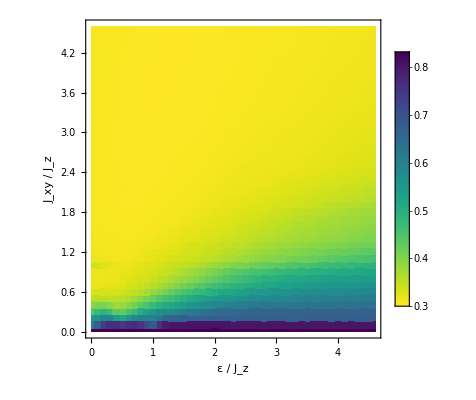

```mathematica
fontSize=22;
fig=ListDensityPlot[choiPurity[[;;last-1]],
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->{Min[#],Max[#]}&[choiPurity[[;;last-1,3]]],
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"ε / J_z","J_xy / J_z"}
]
```

### PNG

```mathematica
filename="figs_ja/temporal_avg_haar_avg_choi_purity_xxz_L_7_Jz_1_omega_0_d_3.png";
Export[filename,fig,"PNG",ImageResolution->300]
```

figs_ja/temporal_avg_haar_avg_choi_purity_xxz_L_7_Jz_1_omega_0_d_3.png

### Nuevo (protocolo)

```mathematica
MinMax[choiPurity[[All,3]]]
```

{0.29178,0.832493}

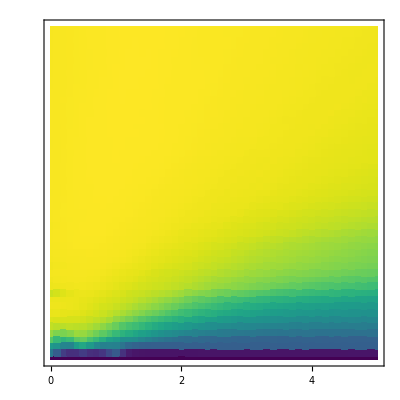

```mathematica
fontSize=32;

fig=ListDensityPlot[choiPurity,
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),
ColorFunctionScaling->True,
PlotRange->{{0.,5},{0.,5},{0.29,0.84}},
PlotRangePadding->0.01,
InterpolationOrder->0,
Frame->True,
FrameStyle->Directive[FontFamily->"Latin Modern Math",FontSize->fontSize,Black,Thick],
FrameTicks->{
{#2,#2},
{#1,#2}
}&[Join[Table[{i,i,0.03,Directive[Black,Thick]},{i,0,5}],Table[{i,None,0.03,Directive[Black,Thick]},{i,0.5,5.5}],Table[{i,None,0.015,Directive[Black,Thick]},{i,0.1,5.9,0.1}]],Join[Table[{i,None,0.03,Directive[Black,Thick]},{i,0,3}],Table[{i,None,0.03,Directive[Black,Thick]},{i,0.5,5.5}],Table[{i,None,0.015,Directive[Black,Thick]},{i,0.1,4.9,0.1}]]],
AspectRatio->1
]
```

```mathematica
filename="figs_ja/temporal_avg_haar_avg_choi_purity/xxz_L_7_Jz_1_omega_0_d_3.pdf";
Export[filename,fig,"PDF",ImageResolution->300]
RunProcess[{"pdfcrop",filename,filename}]
```

figs_ja/temporal_avg_haar_avg_choi_purity/xxz_L_7_Jz_1_omega_0_d_3.pdf

<|ExitCode→0,StandardOutput→PDFCROP 1.42, 2023/04/15 - Copyright (c) 2002-2023 by Heiko Oberdiek, Oberdiek Package Support Group.
==> 1 page written on `figs_ja/temporal_avg_haar_avg_choi_purity/xxz_L_7_Jz_1_omega_0_d_3.pdf'.
,StandardError→|>

```mathematica
fig=BarLegend[{ResourceFunction["ViridisColor"][{0.29,0.84},#]&,{0.29,0.84}},
Ticks->Table[{i,NumberForm[i,{Infinity,2}]},{i,Subdivide[0.29,0.84,2]}],
LegendLayout->"Row",
(*LegendLabel->"⟨(r̃)_n⟩",*)
LabelStyle->Directive[FontFamily->"Latin Modern Math",FontSize->32,Black],
LegendMargins->0,
LegendMarkerSize->{350,20}]
```

```mathematica
filename="figs_ja/temporal_avg_haar_avg_choi_purity/bar_legend_xxz.pdf";
Export[filename,fig,"PDF",ImageResolution->300]
RunProcess[{"pdfcrop",filename,filename}]
```

figs_ja/temporal_avg_haar_avg_choi_purity/bar_legend_xxz.pdf

<|ExitCode→0,StandardOutput→PDFCROP 1.42, 2023/04/15 - Copyright (c) 2002-2023 by Heiko Oberdiek, Oberdiek Package Support Group.
==> 1 page written on `figs_ja/temporal_avg_haar_avg_choi_purity/bar_legend_xxz.pdf'.
,StandardError→|>

## Wisniacki open, h_x=1, barriendo h_z y J (paso = 0.1)

## L=3

```mathematica
L=3;
(* Datos del promedio temporal del valor esperado de Haar de la pureza de Choi *)
{#[[1]],choiPurity=#[[2;;]];}&[Import["data/temporal_haar_avg_choi_purity/wisniacki_open_L_"<>ToString[L]<>"_hx_1.csv"]]
```

{{hz,J,promedio temporal de 0 a 100 del valor esperado de Haar de la pureza de Choi},Null}

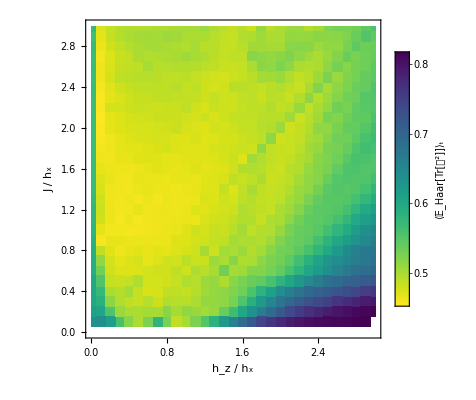

```mathematica
fontSize=18;

fig=ListDensityPlot[choiPurity[[;;961]],
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->{Min[choiPurity[[All,3]]],Max[Select[choiPurity[[All,3]],#<1.&]]},
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨𝔼_Haar[Tr[𝒟^2]]⟩_t",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

```mathematica
filename="figs_ja/temporal_avg_haar_avg_choi_purity/wisniacki_open_L_"<>ToString[L]<>"_hx_1.pdf";
Export[filename,fig,"PDF",ImageResolution->300]
```

figs_ja/temporal_avg_haar_avg_choi_purity/wisniacki_open_L_3_hx_1.pdf

```mathematica
RunProcess[{"pdfcrop",filename,filename}]
```

<|ExitCode→0,StandardOutput→PDFCROP 1.42, 2023/04/15 - Copyright (c) 2002-2023 by Heiko Oberdiek, Oberdiek Package Support Group.
==> 1 page written on `figs_ja/temporal_avg_haar_avg_choi_purity/wisniacki_open_L_3_hx_1.pdf'.
,StandardError→|>

## L=4

```mathematica
L=4;
(* Datos del promedio temporal del valor esperado de Haar de la pureza de Choi *)
{#[[1]],choiPurity=#[[2;;]];}&[Import["data/temporal_haar_avg_choi_purity/wisniacki_open_L_"<>ToString[L]<>"_hx_1.csv"]]
```

{{hz,J,promedio temporal de 0 a 100 del valor esperado de Haar de la pureza de Choi},Null}

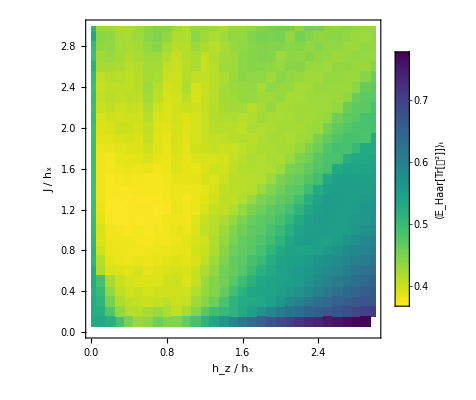

```mathematica
fontSize=18;

fig=ListDensityPlot[choiPurity[[;;961]],
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->{Min[choiPurity[[All,3]]],Max[Select[choiPurity[[All,3]],#<1.&]]},
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨𝔼_Haar[Tr[𝒟^2]]⟩_t",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

```mathematica
filename="figs_ja/temporal_avg_haar_avg_choi_purity/wisniacki_open_L_"<>ToString[L]<>"_hx_1.pdf";
Export[filename,fig,"PDF",ImageResolution->300]
```

figs_ja/temporal_avg_haar_avg_choi_purity/wisniacki_open_L_4_hx_1.pdf

```mathematica
RunProcess[{"pdfcrop",filename,filename}]
```

<|ExitCode→0,StandardOutput→PDFCROP 1.42, 2023/04/15 - Copyright (c) 2002-2023 by Heiko Oberdiek, Oberdiek Package Support Group.
==> 1 page written on `figs_ja/temporal_avg_haar_avg_choi_purity/wisniacki_open_L_4_hx_1.pdf'.
,StandardError→|>

## L=5

```mathematica
L=5;
(* Datos del promedio temporal del valor esperado de Haar de la pureza de Choi *)
{#[[1]],choiPurity=#[[2;;]];}&[Import["data/temporal_haar_avg_choi_purity/wisniacki_open_L_"<>ToString[L]<>"_hx_1.csv"]]
```

{{hz,J,promedio temporal de 0 a 100 del valor esperado de Haar de la pureza de Choi},Null}

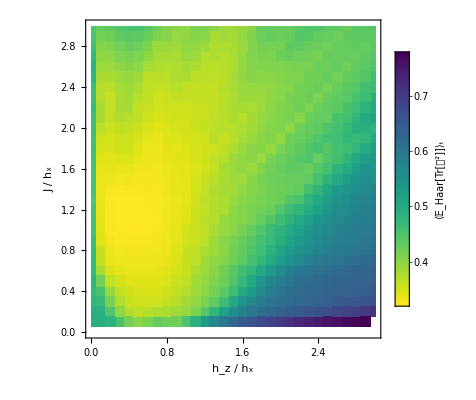

```mathematica
fontSize=18;

fig=ListDensityPlot[choiPurity[[;;961]],
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->{Min[choiPurity[[All,3]]],Max[Select[choiPurity[[All,3]],#<1.&]]},
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨𝔼_Haar[Tr[𝒟^2]]⟩_t",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

```mathematica
filename="figs_ja/temporal_avg_haar_avg_choi_purity/wisniacki_open_L_"<>ToString[L]<>"_hx_1.pdf";
Export[filename,fig,"PDF",ImageResolution->300]
```

figs_ja/temporal_avg_haar_avg_choi_purity/wisniacki_open_L_5_hx_1.pdf

```mathematica
RunProcess[{"pdfcrop",filename,filename}]
```

<|ExitCode→0,StandardOutput→PDFCROP 1.42, 2023/04/15 - Copyright (c) 2002-2023 by Heiko Oberdiek, Oberdiek Package Support Group.
==> 1 page written on `figs_ja/temporal_avg_haar_avg_choi_purity/wisniacki_open_L_5_hx_1.pdf'.
,StandardError→|>

## L=6

```mathematica
L=6;
(* Datos del promedio temporal del valor esperado de Haar de la pureza de Choi *)
{#[[1]],choiPurity=#[[2;;]];}&[Import["data/temporal_haar_avg_choi_purity/wisniacki_open_L_"<>ToString[L]<>"_hx_1.csv"]]
```

{{hz,J,promedio temporal de 0 a 100 del valor esperado de Haar de la pureza de Choi},Null}

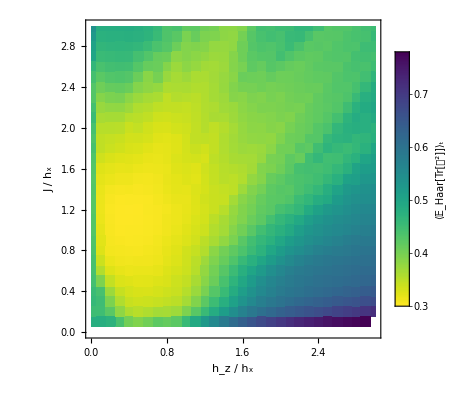

```mathematica
fontSize=18;

fig=ListDensityPlot[choiPurity[[;;961]],
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->{Min[choiPurity[[All,3]]],Max[Select[choiPurity[[All,3]],#<1.&]]},
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨𝔼_Haar[Tr[𝒟^2]]⟩_t",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

```mathematica
filename="figs_ja/temporal_avg_haar_avg_choi_purity/wisniacki_open_L_"<>ToString[L]<>"_hx_1.pdf";
Export[filename,fig,"PDF",ImageResolution->300]
```

figs_ja/temporal_avg_haar_avg_choi_purity/wisniacki_open_L_6_hx_1.pdf

```mathematica
RunProcess[{"pdfcrop",filename,filename}]
```

<|ExitCode→0,StandardOutput→PDFCROP 1.42, 2023/04/15 - Copyright (c) 2002-2023 by Heiko Oberdiek, Oberdiek Package Support Group.
==> 1 page written on `figs_ja/temporal_avg_haar_avg_choi_purity/wisniacki_open_L_6_hx_1.pdf'.
,StandardError→|>

## L=7

```mathematica
(* Datos del promedio temporal del valor esperado de Haar de la pureza de Choi *)
{#[[1]],choiPurity=#[[2;;]];}&[Import["data/temporal_haar_avg_choi_purity/wisniacki_open_L_7_hx_1.csv"]]
```

{{hz,J,promedio temporal de 0 a 100 del valor esperado de Haar de la pureza de Choi},Null}

```mathematica
Flatten[Table[Select[choiPurity,#[[1]]==i&&#[[2]]!=0&],{i,0.1,3,0.1}],1]//Length
```

900

```mathematica
MinMax[Flatten[Table[Select[choiPurity,#[[1]]==i&&#[[2]]!=0&],{i,0.1,3,0.1}],1][[All,3]]]
```

{0.277784,0.784308}

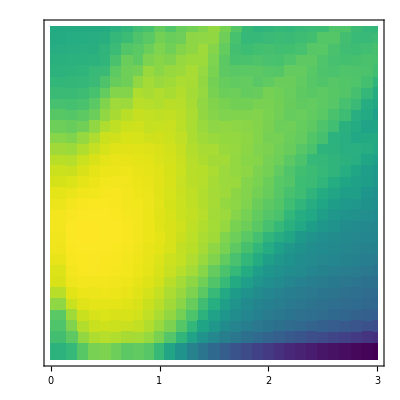

```mathematica
fontSize=32;

fig=ListDensityPlot[Flatten[Table[Select[choiPurity,#[[1]]==i&&#[[2]]!=0&],{i,0.1,3,0.1}],1],
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),
ColorFunctionScaling->True,
(*PlotRange->{Min[choiPurity[[All,3]]],Max[Select[choiPurity[[All,3]],#<1&]]},*)
PlotRange->{{0.,3.0},{0.,3.0}},
PlotRangePadding->0.01,
InterpolationOrder->0,
(*PlotLegends->
Placed[BarLegend[{Automatic,{0.277,0.785}},
Ticks->Table[{i,NumberForm[i,{Infinity,2}]},{i,Subdivide[0.277,0.785,3]}],
LegendLayout->"Row",
(*LegendLabel->Style["𝒫̄",FontSize->fontSize],*)
LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
LegendMargins->0,
LegendMarkerSize->{350,20}]
,Above],*)
PlotLegends->Placed[BarLegend[Automatic,,LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Latin Modern Math",FontSize->fontSize,Black,Thick],
FrameTicks->{
{#2,#2},
{#1,#2}
}&[Join[Table[{i,i,0.03,Directive[Black,Thick]},{i,0,3}],Table[{i,None,0.03,Directive[Black,Thick]},{i,0.5,2.5}],Table[{i,None,0.015,Directive[Black,Thick]},{i,0.1,2.9,0.1}]],Join[Table[{i,None,0.03,Directive[Black,Thick]},{i,0,3}],Table[{i,None,0.03,Directive[Black,Thick]},{i,0.5,2.5}],Table[{i,None,0.015,Directive[Black,Thick]},{i,0.1,2.9,0.1}]]],
(*FrameLabel->{"h_z / h_x",None},*)
AspectRatio->1
]
```

```mathematica
filename="figs_ja/temporal_avg_haar_avg_choi_purity/wisniacki_open_L_7_hx_1.pdf";
Export[filename,fig,"PDF",ImageResolution->300]
RunProcess[{"pdfcrop",filename,filename}]
```

figs_ja/temporal_avg_haar_avg_choi_purity/wisniacki_open_L_7_hx_1.pdf

<|ExitCode→0,StandardOutput→PDFCROP 1.42, 2023/04/15 - Copyright (c) 2002-2023 by Heiko Oberdiek, Oberdiek Package Support Group.
==> 1 page written on `figs_ja/temporal_avg_haar_avg_choi_purity/wisniacki_open_L_7_hx_1.pdf'.
,StandardError→|>

```mathematica
fig=BarLegend[{ResourceFunction["ViridisColor"][{0.277,0.785},#]&,{0.277,0.785}},
Ticks->Table[{i,NumberForm[i,{Infinity,2}]},{i,Subdivide[0.28,0.78,2]}],
LegendLayout->"Row",
(*LegendLabel->"⟨(r̃)_n⟩",*)
LabelStyle->Directive[FontFamily->"Latin Modern Math",FontSize->32,Black],
LegendMargins->0,
LegendMarkerSize->{350,20}]
```

```mathematica
filename="figs_ja/temporal_avg_haar_avg_choi_purity/bar_legend.pdf";
Export[filename,fig,"PDF",ImageResolution->300]
RunProcess[{"pdfcrop",filename,filename}]
```

figs_ja/temporal_avg_haar_avg_choi_purity/bar_legend.pdf

<|ExitCode→0,StandardOutput→PDFCROP 1.42, 2023/04/15 - Copyright (c) 2002-2023 by Heiko Oberdiek, Oberdiek Package Support Group.
==> 1 page written on `figs_ja/temporal_avg_haar_avg_choi_purity/bar_legend.pdf'.
,StandardError→|>

### Comparación con el mapa del mean level spacing ratio

```mathematica
{#[[1;;2]],meanRdata=#[[3;;]];}&[Import["data/mean_level_spacing_ratio/wisniacki_open_L_11_hx_1.csv","CSV"]]
```

{{{# Wisniacki open chain,L=11,hx=1},{h_z/h_x,J/h_x,<r_n>}},Null}

```mathematica
meanRdata//Dimensions
```

{90000,3}

```mathematica
meanRdataSelected=ParallelTable[Select[meanRdata,#[[1;;2]]==i&],{i,Tuples[{#,#}]&[Subdivide[0.,3.,30]]},DistributedContexts->Full];
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{{0.1,0.1,0.431166}},{{0.1,0.2,0.379391}},{{0.1,0.3,0.429964}},{{0.1,0.4,0.465966}},{{0.1,0.5,0.480725}},{{0.1,0.6,0.474181}},{{0.1,0.7,0.511238}},{{0.1,0.8,0.512269}},{{0.1,0.9,0.530222}},{{0.1,1.,0.519184}},{{0.1,1.1,0.506717}},{{0.1,1.2,0.516556}},{{0.1,1.3,0.518364}},{{0.1,1.4,0.482026}},{{0.1,1.5,0.490422}},{{0.1,1.6,0.459377}},{{0.1,1.7,0.443264}},{{0.1,1.8,0.441291}},{{0.1,1.9,0.451621}},{{0.1,2.,0.435947}},{{0.1,2.1,0.43356}},{{0.1,2.2,0.421236}},{{0.1,2.3,0.44016}},{{0.1,2.4,0.446546}},{{0.1,2.5,0.42868}},{{0.1,2.6,0.434124}},{{0.1,2.7,0.450943}},{{0.1,2.8,0.457157}},{{0.1,2.9,0.453231}},{{0.1,3.,0.452438}},{},{{0.2,0.1,0.435086}},{{0.2,0.2,0.429365}},{{0.2,0.3,0.437637}},{{0.2,0.4,0.466343}},{{0.2,0.5,0.506917}},{{0.2,0.6,0.523384}},{{0.2,0.7,0.510163}},{{0.2,0.8,0.505543}},{{0.2,0.9,0.528989}},{{0.2,1.,0.540371}},{{0.2,1.1,0.544395}},{{0.2,1.2,0.503037}},{{0.2,1.3,0.538306}},{{0.2,1.4,0.532186}},{{0.2,1.5,0.513831}},{{0.2,1.6,0.508721}},{{0.2,1.7,0.495675}},{{0.2,1.8,0.474118}},{{0.2,1.9,0.456314}},{{0.2,2.,0.441435}},{{0.2,2.1,0.432855}},{{0.2,2.2,0.422007}},{{0.2,2.3,0.449014}},{{0.2,2.4,0.444514}},{{0.2,2.5,0.452762}},{{0.2,2.6,0.44244}},{{0.2,2.7,0.447688}},{{0.2,2.8,0.452575}},{{0.2,2.9,0.45417}},{{0.2,3.,0.452919}},{},{{0.3,0.1,0.399325}},{{0.3,0.2,0.442537}},{{0.3,0.3,0.45759}},{{0.3,0.4,0.476599}},{{0.3,0.5,0.5031}},{{0.3,0.6,0.515095}},{{0.3,0.7,0.538521}},{{0.3,0.8,0.533875}},{{0.3,0.9,0.535181}},{{0.3,1.,0.543191}},{{0.3,1.1,0.523904}},{{0.3,1.2,0.540139}},{{0.3,1.3,0.524303}},{{0.3,1.4,0.539213}},{{0.3,1.5,0.519263}},{{0.3,1.6,0.512272}},{{0.3,1.7,0.51727}},{{0.3,1.8,0.483222}},{{0.3,1.9,0.49267}},{{0.3,2.,0.481368}},{{0.3,2.1,0.445269}},{{0.3,2.2,0.433382}},{{0.3,2.3,0.428474}},{{0.3,2.4,0.429024}},{{0.3,2.5,0.421031}},{{0.3,2.6,0.437669}},{{0.3,2.7,0.442453}},{{0.3,2.8,0.43814}},{{0.3,2.9,0.454981}},{{0.3,3.,0.461548}},{},{{0.4,0.1,0.428379}},{{0.4,0.2,0.461843}},{{0.4,0.3,0.479821}},{{0.4,0.4,0.509193}},{{0.4,0.5,0.516405}},{{0.4,0.6,0.52838}},{{0.4,0.7,0.529173}},{{0.4,0.8,0.526742}},{{0.4,0.9,0.518484}},{{0.4,1.,0.541722}},{{0.4,1.1,0.53622}},{{0.4,1.2,0.522968}},{{0.4,1.3,0.532934}},{{0.4,1.4,0.541688}},{{0.4,1.5,0.539404}},{{0.4,1.6,0.513681}},{{0.4,1.7,0.513772}},{{0.4,1.8,0.498583}},{{0.4,1.9,0.492927}},{{0.4,2.,0.489112}},{{0.4,2.1,0.458594}},{{0.4,2.2,0.460285}},{{0.4,2.3,0.44491}},{{0.4,2.4,0.445161}},{{0.4,2.5,0.43794}},{{0.4,2.6,0.444332}},{{0.4,2.7,0.438221}},{{0.4,2.8,0.44243}},{{0.4,2.9,0.434898}},{{0.4,3.,0.447481}},{},{{0.5,0.1,0.43143}},{{0.5,0.2,0.464501}},{{0.5,0.3,0.492728}},{{0.5,0.4,0.506533}},{{0.5,0.5,0.502211}},{{0.5,0.6,0.511052}},{{0.5,0.7,0.518807}},{{0.5,0.8,0.53132}},{{0.5,0.9,0.529142}},{{0.5,1.,0.528383}},{{0.5,1.1,0.535304}},{{0.5,1.2,0.531649}},{{0.5,1.3,0.522423}},{{0.5,1.4,0.52383}},{{0.5,1.5,0.525955}},{{0.5,1.6,0.513399}},{{0.5,1.7,0.51727}},{{0.5,1.8,0.502773}},{{0.5,1.9,0.483938}},{{0.5,2.,0.491369}},{{0.5,2.1,0.494728}},{{0.5,2.2,0.47677}},{{0.5,2.3,0.466838}},{{0.5,2.4,0.462706}},{{0.5,2.5,0.434232}},{{0.5,2.6,0.44016}},{{0.5,2.7,0.441459}},{{0.5,2.8,0.444674}},{{0.5,2.9,0.434046}},{{0.5,3.,0.444259}},{},{{0.6,0.1,0.437013}},{{0.6,0.2,0.480852}},{{0.6,0.3,0.499936}},{{0.6,0.4,0.505292}},{{0.6,0.5,0.514308}},{{0.6,0.6,0.521895}},{{0.6,0.7,0.525387}},{{0.6,0.8,0.520669}},{{0.6,0.9,0.517214}},{{0.6,1.,0.526673}},{{0.6,1.1,0.545862}},{{0.6,1.2,0.518403}},{{0.6,1.3,0.522668}},{{0.6,1.4,0.531377}},{{0.6,1.5,0.528574}},{{0.6,1.6,0.526409}},{{0.6,1.7,0.533629}},{{0.6,1.8,0.499526}},{{0.6,1.9,0.502687}},{{0.6,2.,0.504175}},{{0.6,2.1,0.499411}},{{0.6,2.2,0.465412}},{{0.6,2.3,0.48274}},{{0.6,2.4,0.47009}},{{0.6,2.5,0.454693}},{{0.6,2.6,0.445715}},{{0.6,2.7,0.427321}},{{0.6,2.8,0.431723}},{{0.6,2.9,0.430645}},{{0.6,3.,0.433223}},{},{{0.7,0.1,0.449167}},{{0.7,0.2,0.474712}},{{0.7,0.3,0.492013}},{{0.7,0.4,0.511888}},{{0.7,0.5,0.525965}},{{0.7,0.6,0.510855}},{{0.7,0.7,0.510966}},{{0.7,0.8,0.524634}},{{0.7,0.9,0.517785}},{{0.7,1.,0.520953}},{{0.7,1.1,0.514484}},{{0.7,1.2,0.539681}},{{0.7,1.3,0.521118}},{{0.7,1.4,0.512273}},{{0.7,1.5,0.521376}},{{0.7,1.6,0.515293}},{{0.7,1.7,0.514846}},{{0.7,1.8,0.522878}},{{0.7,1.9,0.50459}},{{0.7,2.,0.499703}},{{0.7,2.1,0.483517}},{{0.7,2.2,0.471595}},{{0.7,2.3,0.463908}},{{0.7,2.4,0.461841}},{{0.7,2.5,0.470583}},{{0.7,2.6,0.456953}},{{0.7,2.7,0.463342}},{{0.7,2.8,0.441668}},{{0.7,2.9,0.446042}},{{0.7,3.,0.43251}},{},{{0.8,0.1,0.421348}},{{0.8,0.2,0.455484}},{{0.8,0.3,0.479095}},{{0.8,0.4,0.489121}},{{0.8,0.5,0.514868}},{{0.8,0.6,0.51472}},{{0.8,0.7,0.522641}},{{0.8,0.8,0.53169}},{{0.8,0.9,0.532156}},{{0.8,1.,0.523226}},{{0.8,1.1,0.529246}},{{0.8,1.2,0.520535}},{{0.8,1.3,0.506945}},{{0.8,1.4,0.528422}},{{0.8,1.5,0.514077}},{{0.8,1.6,0.514532}},{{0.8,1.7,0.50122}},{{0.8,1.8,0.50559}},{{0.8,1.9,0.494404}},{{0.8,2.,0.485684}},{{0.8,2.1,0.49534}},{{0.8,2.2,0.504157}},{{0.8,2.3,0.479772}},{{0.8,2.4,0.476692}},{{0.8,2.5,0.455895}},{{0.8,2.6,0.468263}},{{0.8,2.7,0.43581}},{{0.8,2.8,0.46065}},{{0.8,2.9,0.448336}},{{0.8,3.,0.448972}},{},{{0.9,0.1,0.429557}},{{0.9,0.2,0.433105}},{{0.9,0.3,0.48053}},{{0.9,0.4,0.47833}},{{0.9,0.5,0.490255}},{{0.9,0.6,0.506932}},{{0.9,0.7,0.531903}},{{0.9,0.8,0.512247}},{{0.9,0.9,0.53539}},{{0.9,1.,0.527836}},{{0.9,1.1,0.497054}},{{0.9,1.2,0.528505}},{{0.9,1.3,0.520391}},{{0.9,1.4,0.52177}},{{0.9,1.5,0.507641}},{{0.9,1.6,0.512697}},{{0.9,1.7,0.510062}},{{0.9,1.8,0.504333}},{{0.9,1.9,0.500089}},{{0.9,2.,0.488565}},{{0.9,2.1,0.467375}},{{0.9,2.2,0.475789}},{{0.9,2.3,0.474359}},{{0.9,2.4,0.462774}},{{0.9,2.5,0.461021}},{{0.9,2.6,0.458307}},{{0.9,2.7,0.452937}},{{0.9,2.8,0.450263}},{{0.9,2.9,0.453275}},{{0.9,3.,0.425194}},{},{{1.,0.1,0.429971}},{{1.,0.2,0.436887}},{{1.,0.3,0.463574}},{{1.,0.4,0.468316}},{{1.,0.5,0.480922}},{{1.,0.6,0.494771}},{{1.,0.7,0.491851}},{{1.,0.8,0.515504}},{{1.,0.9,0.506961}},{{1.,1.,0.518369}},{{1.,1.1,0.531752}},{{1.,1.2,0.52269}},{{1.,1.3,0.498498}},{{1.,1.4,0.518416}},{{1.,1.5,0.508737}},{{1.,1.6,0.519535}},{{1.,1.7,0.500411}},{{1.,1.8,0.498311}},{{1.,1.9,0.493281}},{{1.,2.,0.489371}},{{1.,2.1,0.477294}},{{1.,2.2,0.476369}},{{1.,2.3,0.468081}},{{1.,2.4,0.479533}},{{1.,2.5,0.470909}},{{1.,2.6,0.483523}},{{1.,2.7,0.44941}},{{1.,2.8,0.448238}},{{1.,2.9,0.46173}},{{1.,3.,0.454349}},{},{{1.1,0.1,0.411538}},{{1.1,0.2,0.418344}},{{1.1,0.3,0.458348}},{{1.1,0.4,0.469506}},{{1.1,0.5,0.457606}},{{1.1,0.6,0.474275}},{{1.1,0.7,0.496074}},{{1.1,0.8,0.504767}},{{1.1,0.9,0.498598}},{{1.1,1.,0.505066}},{{1.1,1.1,0.499241}},{{1.1,1.2,0.49243}},{{1.1,1.3,0.514461}},{{1.1,1.4,0.506045}},{{1.1,1.5,0.486789}},{{1.1,1.6,0.498018}},{{1.1,1.7,0.496522}},{{1.1,1.8,0.49249}},{{1.1,1.9,0.476459}},{{1.1,2.,0.47957}},{{1.1,2.1,0.488788}},{{1.1,2.2,0.491394}},{{1.1,2.3,0.465767}},{{1.1,2.4,0.476338}},{{1.1,2.5,0.465204}},{{1.1,2.6,0.451364}},{{1.1,2.7,0.454889}},{{1.1,2.8,0.461348}},{{1.1,2.9,0.457105}},{{1.1,3.,0.446041}},{},{{1.2,0.1,0.402843}},{{1.2,0.2,0.425345}},{{1.2,0.3,0.438188}},{{1.2,0.4,0.457656}},{{1.2,0.5,0.434672}},{{1.2,0.6,0.460065}},{{1.2,0.7,0.480092}},{{1.2,0.8,0.487836}},{{1.2,0.9,0.49664}},{{1.2,1.,0.520586}},{{1.2,1.1,0.509702}},{{1.2,1.2,0.49804}},{{1.2,1.3,0.493393}},{{1.2,1.4,0.493574}},{{1.2,1.5,0.494259}},{{1.2,1.6,0.481463}},{{1.2,1.7,0.485984}},{{1.2,1.8,0.491737}},{{1.2,1.9,0.470311}},{{1.2,2.,0.468875}},{{1.2,2.1,0.482939}},{{1.2,2.2,0.483861}},{{1.2,2.3,0.481536}},{{1.2,2.4,0.467228}},{{1.2,2.5,0.471924}},{{1.2,2.6,0.46107}},{{1.2,2.7,0.448431}},{{1.2,2.8,0.458777}},{{1.2,2.9,0.449157}},{{1.2,3.,0.450492}},{},{{1.3,0.1,0.393142}},{{1.3,0.2,0.410082}},{{1.3,0.3,0.42612}},{{1.3,0.4,0.454884}},{{1.3,0.5,0.447566}},{{1.3,0.6,0.455539}},{{1.3,0.7,0.46721}},{{1.3,0.8,0.475432}},{{1.3,0.9,0.480829}},{{1.3,1.,0.508009}},{{1.3,1.1,0.507597}},{{1.3,1.2,0.49012}},{{1.3,1.3,0.495006}},{{1.3,1.4,0.482791}},{{1.3,1.5,0.493484}},{{1.3,1.6,0.479385}},{{1.3,1.7,0.48534}},{{1.3,1.8,0.491343}},{{1.3,1.9,0.483915}},{{1.3,2.,0.469097}},{{1.3,2.1,0.465102}},{{1.3,2.2,0.479778}},{{1.3,2.3,0.458119}},{{1.3,2.4,0.471697}},{{1.3,2.5,0.471444}},{{1.3,2.6,0.471363}},{{1.3,2.7,0.466745}},{{1.3,2.8,0.463898}},{{1.3,2.9,0.457015}},{{1.3,3.,0.452967}},{},{{1.4,0.1,0.400677}},{{1.4,0.2,0.417541}},{{1.4,0.3,0.413494}},{{1.4,0.4,0.43266}},{{1.4,0.5,0.436034}},{{1.4,0.6,0.438805}},{{1.4,0.7,0.454523}},{{1.4,0.8,0.447402}},{{1.4,0.9,0.451883}},{{1.4,1.,0.48511}},{{1.4,1.1,0.478151}},{{1.4,1.2,0.495887}},{{1.4,1.3,0.491082}},{{1.4,1.4,0.459497}},{{1.4,1.5,0.458799}},{{1.4,1.6,0.475015}},{{1.4,1.7,0.471813}},{{1.4,1.8,0.457451}},{{1.4,1.9,0.478248}},{{1.4,2.,0.479653}},{{1.4,2.1,0.463486}},{{1.4,2.2,0.460992}},{{1.4,2.3,0.472504}},{{1.4,2.4,0.467401}},{{1.4,2.5,0.454744}},{{1.4,2.6,0.470991}},{{1.4,2.7,0.461091}},{{1.4,2.8,0.463858}},{{1.4,2.9,0.472398}},{{1.4,3.,0.441692}},{},{{1.5,0.1,0.397833}},{{1.5,0.2,0.416894}},{{1.5,0.3,0.421833}},{{1.5,0.4,0.425197}},{{1.5,0.5,0.415809}},{{1.5,0.6,0.412463}},{{1.5,0.7,0.425762}},{{1.5,0.8,0.44247}},{{1.5,0.9,0.461105}},{{1.5,1.,0.465569}},{{1.5,1.1,0.476802}},{{1.5,1.2,0.487212}},{{1.5,1.3,0.491129}},{{1.5,1.4,0.474044}},{{1.5,1.5,0.453899}},{{1.5,1.6,0.458556}},{{1.5,1.7,0.459263}},{{1.5,1.8,0.479595}},{{1.5,1.9,0.467577}},{{1.5,2.,0.462584}},{{1.5,2.1,0.466358}},{{1.5,2.2,0.464346}},{{1.5,2.3,0.465928}},{{1.5,2.4,0.470016}},{{1.5,2.5,0.455792}},{{1.5,2.6,0.448966}},{{1.5,2.7,0.454029}},{{1.5,2.8,0.465401}},{{1.5,2.9,0.458124}},{{1.5,3.,0.455945}},{},{{1.6,0.1,0.389885}},{{1.6,0.2,0.416519}},{{1.6,0.3,0.423366}},{{1.6,0.4,0.43101}},{{1.6,0.5,0.419335}},{{1.6,0.6,0.423715}},{{1.6,0.7,0.431589}},{{1.6,0.8,0.437757}},{{1.6,0.9,0.43842}},{{1.6,1.,0.456237}},{{1.6,1.1,0.46114}},{{1.6,1.2,0.461036}},{{1.6,1.3,0.457645}},{{1.6,1.4,0.480316}},{{1.6,1.5,0.452586}},{{1.6,1.6,0.451845}},{{1.6,1.7,0.457228}},{{1.6,1.8,0.450513}},{{1.6,1.9,0.465499}},{{1.6,2.,0.458227}},{{1.6,2.1,0.446172}},{{1.6,2.2,0.471519}},{{1.6,2.3,0.45682}},{{1.6,2.4,0.453364}},{{1.6,2.5,0.440681}},{{1.6,2.6,0.458962}},{{1.6,2.7,0.457177}},{{1.6,2.8,0.459353}},{{1.6,2.9,0.461523}},{{1.6,3.,0.465593}},{},{{1.7,0.1,0.390018}},{{1.7,0.2,0.419603}},{{1.7,0.3,0.422858}},{{1.7,0.4,0.438348}},{{1.7,0.5,0.427106}},{{1.7,0.6,0.406709}},{{1.7,0.7,0.428142}},{{1.7,0.8,0.427674}},{{1.7,0.9,0.429855}},{{1.7,1.,0.440307}},{{1.7,1.1,0.444203}},{{1.7,1.2,0.468122}},{{1.7,1.3,0.481245}},{{1.7,1.4,0.457104}},{{1.7,1.5,0.45642}},{{1.7,1.6,0.462477}},{{1.7,1.7,0.450655}},{{1.7,1.8,0.460471}},{{1.7,1.9,0.462244}},{{1.7,2.,0.457719}},{{1.7,2.1,0.466854}},{{1.7,2.2,0.463337}},{{1.7,2.3,0.458394}},{{1.7,2.4,0.453282}},{{1.7,2.5,0.451114}},{{1.7,2.6,0.460592}},{{1.7,2.7,0.456892}},{{1.7,2.8,0.448114}},{{1.7,2.9,0.434498}},{{1.7,3.,0.431477}},{},{{1.8,0.1,0.388568}},{{1.8,0.2,0.412731}},{{1.8,0.3,0.42314}},{{1.8,0.4,0.42411}},{{1.8,0.5,0.408949}},{{1.8,0.6,0.41845}},{{1.8,0.7,0.417912}},{{1.8,0.8,0.416102}},{{1.8,0.9,0.418635}},{{1.8,1.,0.419003}},{{1.8,1.1,0.44763}},{{1.8,1.2,0.467892}},{{1.8,1.3,0.468992}},{{1.8,1.4,0.467391}},{{1.8,1.5,0.435283}},{{1.8,1.6,0.463058}},{{1.8,1.7,0.434478}},{{1.8,1.8,0.450928}},{{1.8,1.9,0.448807}},{{1.8,2.,0.445304}},{{1.8,2.1,0.454512}},{{1.8,2.2,0.453011}},{{1.8,2.3,0.455163}},{{1.8,2.4,0.448746}},{{1.8,2.5,0.459123}},{{1.8,2.6,0.457142}},{{1.8,2.7,0.457524}},{{1.8,2.8,0.45215}},{{1.8,2.9,0.427071}},{{1.8,3.,0.432022}},{},{{1.9,0.1,0.397533}},{{1.9,0.2,0.406902}},{{1.9,0.3,0.421402}},{{1.9,0.4,0.419966}},{{1.9,0.5,0.415937}},{{1.9,0.6,0.42342}},{{1.9,0.7,0.430187}},{{1.9,0.8,0.409874}},{{1.9,0.9,0.425115}},{{1.9,1.,0.426245}},{{1.9,1.1,0.434374}},{{1.9,1.2,0.444}},{{1.9,1.3,0.452701}},{{1.9,1.4,0.447905}},{{1.9,1.5,0.4493}},{{1.9,1.6,0.438764}},{{1.9,1.7,0.436673}},{{1.9,1.8,0.451456}},{{1.9,1.9,0.471783}},{{1.9,2.,0.454757}},{{1.9,2.1,0.44813}},{{1.9,2.2,0.439067}},{{1.9,2.3,0.465975}},{{1.9,2.4,0.455494}},{{1.9,2.5,0.444335}},{{1.9,2.6,0.454221}},{{1.9,2.7,0.462746}},{{1.9,2.8,0.441979}},{{1.9,2.9,0.459494}},{{1.9,3.,0.43485}},{},{{2.,0.1,0.383708}},{{2.,0.2,0.41269}},{{2.,0.3,0.410518}},{{2.,0.4,0.406296}},{{2.,0.5,0.409317}},{{2.,0.6,0.409566}},{{2.,0.7,0.421347}},{{2.,0.8,0.425309}},{{2.,0.9,0.403582}},{{2.,1.,0.408143}},{{2.,1.1,0.430219}},{{2.,1.2,0.43083}},{{2.,1.3,0.447831}},{{2.,1.4,0.430474}},{{2.,1.5,0.440018}},{{2.,1.6,0.44126}},{{2.,1.7,0.451894}},{{2.,1.8,0.42847}},{{2.,1.9,0.446553}},{{2.,2.,0.445318}},{{2.,2.1,0.449664}},{{2.,2.2,0.448533}},{{2.,2.3,0.42578}},{{2.,2.4,0.457132}},{{2.,2.5,0.463846}},{{2.,2.6,0.436417}},{{2.,2.7,0.429952}},{{2.,2.8,0.430718}},{{2.,2.9,0.455112}},{{2.,3.,0.465337}},{},{{2.1,0.1,0.378922}},{{2.1,0.2,0.415596}},{{2.1,0.3,0.405753}},{{2.1,0.4,0.413214}},{{2.1,0.5,0.402579}},{{2.1,0.6,0.40703}},{{2.1,0.7,0.416498}},{{2.1,0.8,0.42195}},{{2.1,0.9,0.40806}},{{2.1,1.,0.407606}},{{2.1,1.1,0.42363}},{{2.1,1.2,0.430801}},{{2.1,1.3,0.451175}},{{2.1,1.4,0.431216}},{{2.1,1.5,0.446733}},{{2.1,1.6,0.423456}},{{2.1,1.7,0.440191}},{{2.1,1.8,0.446315}},{{2.1,1.9,0.456354}},{{2.1,2.,0.445543}},{{2.1,2.1,0.449444}},{{2.1,2.2,0.441875}},{{2.1,2.3,0.46599}},{{2.1,2.4,0.449525}},{{2.1,2.5,0.455954}},{{2.1,2.6,0.45147}},{{2.1,2.7,0.442094}},{{2.1,2.8,0.434404}},{{2.1,2.9,0.442826}},{{2.1,3.,0.457777}},{},{{2.2,0.1,0.373585}},{{2.2,0.2,0.410876}},{{2.2,0.3,0.401849}},{{2.2,0.4,0.410387}},{{2.2,0.5,0.402393}},{{2.2,0.6,0.40296}},{{2.2,0.7,0.403034}},{{2.2,0.8,0.413161}},{{2.2,0.9,0.414317}},{{2.2,1.,0.417479}},{{2.2,1.1,0.417918}},{{2.2,1.2,0.428628}},{{2.2,1.3,0.432174}},{{2.2,1.4,0.417695}},{{2.2,1.5,0.442639}},{{2.2,1.6,0.427412}},{{2.2,1.7,0.428667}},{{2.2,1.8,0.43223}},{{2.2,1.9,0.43761}},{{2.2,2.,0.453355}},{{2.2,2.1,0.438842}},{{2.2,2.2,0.452834}},{{2.2,2.3,0.432728}},{{2.2,2.4,0.460233}},{{2.2,2.5,0.445686}},{{2.2,2.6,0.463908}},{{2.2,2.7,0.437187}},{{2.2,2.8,0.445877}},{{2.2,2.9,0.436964}},{{2.2,3.,0.420669}},{},{{2.3,0.1,0.36476}},{{2.3,0.2,0.406988}},{{2.3,0.3,0.400827}},{{2.3,0.4,0.402983}},{{2.3,0.5,0.408981}},{{2.3,0.6,0.403244}},{{2.3,0.7,0.412155}},{{2.3,0.8,0.41401}},{{2.3,0.9,0.409184}},{{2.3,1.,0.404163}},{{2.3,1.1,0.407398}},{{2.3,1.2,0.428022}},{{2.3,1.3,0.433509}},{{2.3,1.4,0.429907}},{{2.3,1.5,0.432164}},{{2.3,1.6,0.444604}},{{2.3,1.7,0.432905}},{{2.3,1.8,0.447263}},{{2.3,1.9,0.439099}},{{2.3,2.,0.432925}},{{2.3,2.1,0.446021}},{{2.3,2.2,0.459578}},{{2.3,2.3,0.451412}},{{2.3,2.4,0.446962}},{{2.3,2.5,0.4587}},{{2.3,2.6,0.452388}},{{2.3,2.7,0.450693}},{{2.3,2.8,0.459271}},{{2.3,2.9,0.455417}},{{2.3,3.,0.432212}},{},{{2.4,0.1,0.361063}},{{2.4,0.2,0.396118}},{{2.4,0.3,0.397158}},{{2.4,0.4,0.403872}},{{2.4,0.5,0.409238}},{{2.4,0.6,0.391957}},{{2.4,0.7,0.418829}},{{2.4,0.8,0.400901}},{{2.4,0.9,0.408381}},{{2.4,1.,0.413067}},{{2.4,1.1,0.405853}},{{2.4,1.2,0.409325}},{{2.4,1.3,0.403936}},{{2.4,1.4,0.428878}},{{2.4,1.5,0.419219}},{{2.4,1.6,0.417049}},{{2.4,1.7,0.435878}},{{2.4,1.8,0.42763}},{{2.4,1.9,0.438252}},{{2.4,2.,0.425771}},{{2.4,2.1,0.433762}},{{2.4,2.2,0.465212}},{{2.4,2.3,0.443938}},{{2.4,2.4,0.443119}},{{2.4,2.5,0.449868}},{{2.4,2.6,0.463532}},{{2.4,2.7,0.457503}},{{2.4,2.8,0.438979}},{{2.4,2.9,0.455679}},{{2.4,3.,0.427679}},{},{{2.5,0.1,0.364163}},{{2.5,0.2,0.388182}},{{2.5,0.3,0.392244}},{{2.5,0.4,0.3998}},{{2.5,0.5,0.4127}},{{2.5,0.6,0.396189}},{{2.5,0.7,0.413331}},{{2.5,0.8,0.41112}},{{2.5,0.9,0.404152}},{{2.5,1.,0.403827}},{{2.5,1.1,0.409979}},{{2.5,1.2,0.417632}},{{2.5,1.3,0.433737}},{{2.5,1.4,0.422383}},{{2.5,1.5,0.410804}},{{2.5,1.6,0.434359}},{{2.5,1.7,0.440633}},{{2.5,1.8,0.431636}},{{2.5,1.9,0.434016}},{{2.5,2.,0.428083}},{{2.5,2.1,0.429906}},{{2.5,2.2,0.419847}},{{2.5,2.3,0.444238}},{{2.5,2.4,0.466278}},{{2.5,2.5,0.438418}},{{2.5,2.6,0.456982}},{{2.5,2.7,0.442951}},{{2.5,2.8,0.45839}},{{2.5,2.9,0.44497}},{{2.5,3.,0.442099}},{},{{2.6,0.1,0.360494}},{{2.6,0.2,0.386353}},{{2.6,0.3,0.391956}},{{2.6,0.4,0.396234}},{{2.6,0.5,0.406487}},{{2.6,0.6,0.401277}},{{2.6,0.7,0.413292}},{{2.6,0.8,0.399041}},{{2.6,0.9,0.401615}},{{2.6,1.,0.402309}},{{2.6,1.1,0.421245}},{{2.6,1.2,0.415586}},{{2.6,1.3,0.418415}},{{2.6,1.4,0.409667}},{{2.6,1.5,0.424589}},{{2.6,1.6,0.42218}},{{2.6,1.7,0.429933}},{{2.6,1.8,0.428177}},{{2.6,1.9,0.434404}},{{2.6,2.,0.426655}},{{2.6,2.1,0.417059}},{{2.6,2.2,0.431064}},{{2.6,2.3,0.434195}},{{2.6,2.4,0.455649}},{{2.6,2.5,0.462232}},{{2.6,2.6,0.436696}},{{2.6,2.7,0.454127}},{{2.6,2.8,0.450504}},{{2.6,2.9,0.458291}},{{2.6,3.,0.44488}},{},{{2.7,0.1,0.355807}},{{2.7,0.2,0.381129}},{{2.7,0.3,0.394867}},{{2.7,0.4,0.389504}},{{2.7,0.5,0.401582}},{{2.7,0.6,0.39863}},{{2.7,0.7,0.416622}},{{2.7,0.8,0.401759}},{{2.7,0.9,0.390076}},{{2.7,1.,0.404707}},{{2.7,1.1,0.413544}},{{2.7,1.2,0.413969}},{{2.7,1.3,0.424138}},{{2.7,1.4,0.419363}},{{2.7,1.5,0.409525}},{{2.7,1.6,0.407704}},{{2.7,1.7,0.427861}},{{2.7,1.8,0.436713}},{{2.7,1.9,0.434316}},{{2.7,2.,0.414608}},{{2.7,2.1,0.420167}},{{2.7,2.2,0.430973}},{{2.7,2.3,0.424319}},{{2.7,2.4,0.430562}},{{2.7,2.5,0.456791}},{{2.7,2.6,0.460948}},{{2.7,2.7,0.440498}},{{2.7,2.8,0.433148}},{{2.7,2.9,0.446449}},{{2.7,3.,0.445106}},{},{{2.8,0.1,0.3536}},{{2.8,0.2,0.379825}},{{2.8,0.3,0.387393}},{{2.8,0.4,0.390801}},{{2.8,0.5,0.396626}},{{2.8,0.6,0.389736}},{{2.8,0.7,0.395416}},{{2.8,0.8,0.407281}},{{2.8,0.9,0.396975}},{{2.8,1.,0.399866}},{{2.8,1.1,0.407497}},{{2.8,1.2,0.407189}},{{2.8,1.3,0.403661}},{{2.8,1.4,0.411944}},{{2.8,1.5,0.413268}},{{2.8,1.6,0.416364}},{{2.8,1.7,0.402812}},{{2.8,1.8,0.416893}},{{2.8,1.9,0.422371}},{{2.8,2.,0.418956}},{{2.8,2.1,0.421161}},{{2.8,2.2,0.426279}},{{2.8,2.3,0.420533}},{{2.8,2.4,0.417516}},{{2.8,2.5,0.444257}},{{2.8,2.6,0.451426}},{{2.8,2.7,0.437076}},{{2.8,2.8,0.437717}},{{2.8,2.9,0.435597}},{{2.8,3.,0.442365}},{},{{2.9,0.1,0.348755}},{{2.9,0.2,0.37359}},{{2.9,0.3,0.380408}},{{2.9,0.4,0.38941}},{{2.9,0.5,0.387135}},{{2.9,0.6,0.383315}},{{2.9,0.7,0.39186}},{{2.9,0.8,0.401712}},{{2.9,0.9,0.390867}},{{2.9,1.,0.403247}},{{2.9,1.1,0.402824}},{{2.9,1.2,0.411037}},{{2.9,1.3,0.390831}},{{2.9,1.4,0.410302}},{{2.9,1.5,0.421135}},{{2.9,1.6,0.420503}},{{2.9,1.7,0.418089}},{{2.9,1.8,0.408688}},{{2.9,1.9,0.415695}},{{2.9,2.,0.426453}},{{2.9,2.1,0.395928}},{{2.9,2.2,0.418999}},{{2.9,2.3,0.415553}},{{2.9,2.4,0.419376}},{{2.9,2.5,0.434861}},{{2.9,2.6,0.44763}},{{2.9,2.7,0.423118}},{{2.9,2.8,0.436795}},{{2.9,2.9,0.438362}},{{2.9,3.,0.438788}},{},{{3.,0.1,0.348582}},{{3.,0.2,0.368059}},{{3.,0.3,0.376828}},{{3.,0.4,0.380849}},{{3.,0.5,0.390195}},{{3.,0.6,0.377382}},{{3.,0.7,0.387458}},{{3.,0.8,0.409926}},{{3.,0.9,0.393514}},{{3.,1.,0.397008}},{{3.,1.1,0.394299}},{{3.,1.2,0.40176}},{{3.,1.3,0.39558}},{{3.,1.4,0.40465}},{{3.,1.5,0.40851}},{{3.,1.6,0.404565}},{{3.,1.7,0.424769}},{{3.,1.8,0.413893}},{{3.,1.9,0.398685}},{{3.,2.,0.410217}},{{3.,2.1,0.422851}},{{3.,2.2,0.413423}},{{3.,2.3,0.422687}},{{3.,2.4,0.412618}},{{3.,2.5,0.407731}},{{3.,2.6,0.432432}},{{3.,2.7,0.431206}},{{3.,2.8,0.444555}},{{3.,2.9,0.435963}},{{3.,3.,0.443658}}}

```mathematica
meanRdataSelected=Flatten[meanRdataSelected,1];
```

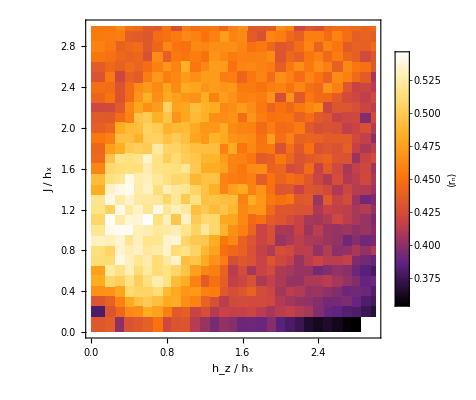

```mathematica
fontSize=22;
fig=
ListDensityPlot[meanRdataSelected,
InterpolationOrder->0,ColorFunction->"SunsetColors",
PlotRange->{0.35,0.55},
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨r_n⟩",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"}]
```

### Comparación

```mathematica
LogSpace[start_,end_,n_]:=Exp@Subdivide[Log[start],Log[end],n-1]
```

```mathematica
tiempos=LogSpace[0.1,1000,100];
```

```mathematica
points = Tuples[Join[Flatten[Table[Subdivide[#[[i]],#[[i+1]],3][[1;;3]],{i,9}]],{2.95}],2]&[Subdivide[0.05,2.95,9]];
```

```mathematica
map={};

Do[
haarAvg=Import["data/haar_avg_choi_purity/wisniacki/open/L_7/hx_1_hz_"<>ToString[NumberForm[i[[1]],{Infinity,2}]]<>"_J_"<>ToString[NumberForm[i[[2]],{Infinity,2}]]<>".csv","CSV"][[2;;]];

(* Calcular promedio temporal *)
purityInterp = Interpolation[haarAvg]; 
tmpAvg=NIntegrate[purityInterp[t],{t,tiempos[[-100]],tiempos[[-1]]}]/(tiempos[[-1]]-tiempos[[-100]]);

AppendTo[map,{i[[1]],i[[2]],tmpAvg}]

,{i,points}]
```

```mathematica
map2=ArrayReshape[map,{3,100,3}];
```

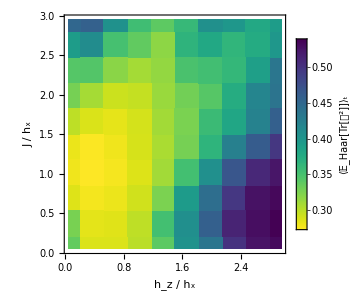
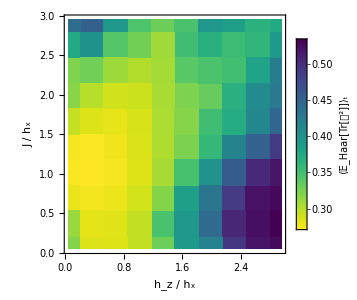
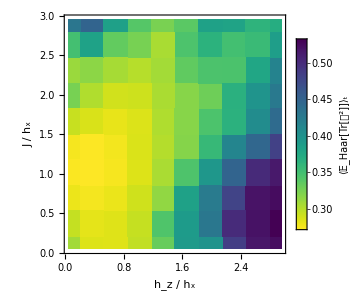

```mathematica
fontSize=18;

ListDensityPlot[#,
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨𝔼_Haar[Tr[𝒟^2]]⟩_t",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1,
ImageSize->300
]&/@map2
```

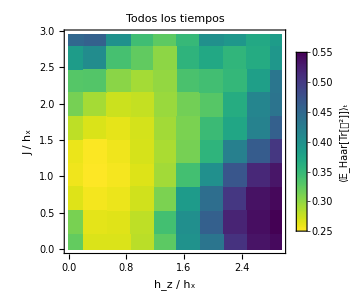
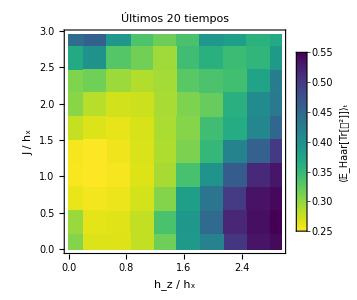
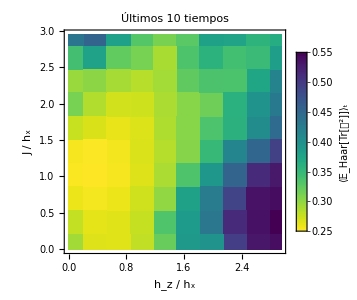

```mathematica
fontSize=18;

fig=ListDensityPlot[#[[1]],
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->{0.25,0.55},
InterpolationOrder->0,
PlotLegends->
Placed[
BarLegend[{Automatic,{0.25,0.55}},
LegendLabel->Style["⟨𝔼_Haar[Tr[𝒟^2]]⟩_t",FontSize->14],LabelStyle->Directive[FontFamily->"Arial",FontSize->16,Black],LegendMarkerSize->{20, 250}
]
,Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1,
ImageSize->300,
PlotLabel->Style[#[[2]],Black,FontSize->fontSize]
]&/@{{map2[[1]],"Todos los tiempos"},{map2[[2]],"Últimos 20 tiempos"},{map2[[3]],"Últimos 10 tiempos"}}
```

```mathematica
GraphicsGrid[{fig},
Spacings->{-170,0},
ImageSize->Full]
```

-Graphics-

```mathematica
p=Subdivide[0.05,2.95,9]
```

{0.05,0.372222,0.694444,1.01667,1.33889,1.66111,1.98333,2.30556,2.62778,2.95}

```mathematica
Length[newPoints=Tuples[Join[Flatten[Table[Subdivide[p[[i]],p[[i+1]],3][[1;;3]],{i,9}]],{2.95}],2]]
```

784

```mathematica
missingPoints=Complement[newPoints,points];
```

### Estados productos aleatorio

```mathematica
Get["../Mathematica_packages/QMB.wl"]
```

```mathematica
LogSpace[start_,end_,n_]:=Exp@Subdivide[Log[start],Log[end],n-1]
```

```mathematica
tiempos=LogSpace[0.1,1000,100];
```

```mathematica
{t0,tf}={0.1,1000}
```

{0.1,1000}

```mathematica
points = Tuples[Join[Flatten[Table[Subdivide[#[[i]],#[[i+1]],3][[1;;3]],{i,9}]],{2.95}],2]&[Subdivide[0.05,2.95,9]];
```

```mathematica
tmpAvgpurities={};

LaunchKernels[6];
SetSharedVariable[tmpAvgpurities];SetSharedFunction[Purity];
ParallelDo[
chois=Import["data/chois/wisniacki_Jt/L_7_hx_1_hz_"<>ToString[NumberForm[i[[1]],{Infinity,2}]]<>"_J_"<>ToString[NumberForm[i[[2]],{Infinity,2}]]<>"/"<>StringPadLeft[ToString[#],3,"0"]<>".mat","MAT"][[1,2;;]]&/@Range[100];

(* Reconstruir las matrices de Choi *)
chois=ArrayReshape[chois,{100,4,4}];

purities=Chop[Purity/@chois];

(* Calcular promedio temporal *)
purityInterp = Interpolation[Transpose[{tiempos,purities}]]; 
tmpAvg=NIntegrate[purityInterp[t],{t,t0,tf}]/(tf-t0);
AppendTo[tmpAvgpurities,{i[[1]],i[[2]],tmpAvg}];

,{i,points}]
CloseKernels[];
```

```mathematica
p=Table[Join[points[[i]],{tmpAvgpurities[[i]]}],{i,784}];
```

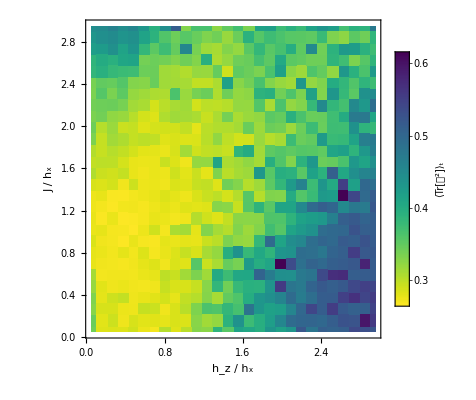

```mathematica
fontSize=18;

fig=ListDensityPlot[p,
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨Tr[𝒟^2]⟩_t",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

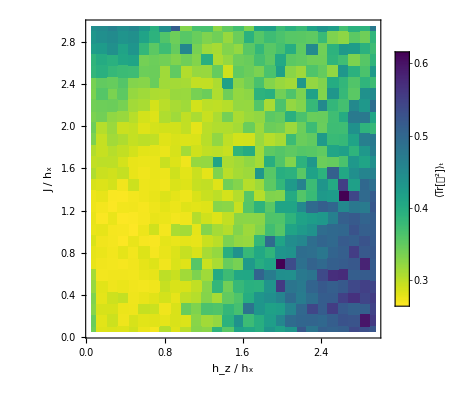

```mathematica
fontSize=18;

fig=ListDensityPlot[tmpAvgpurities,
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨Tr[𝒟^2]⟩_t",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

```mathematica
Export["~/Documents/chaos_meets_channels/ja_files/figs_ja/temporalAvg_choiPurity_AvgOverInitialProductStates_wisniacki_L_7_h_1.pdf",fig,"PDF"]
```

~/Documents/chaos_meets_channels/ja_files/figs_ja/temporalAvg_choiPurity_AvgOverInitialProductStates_wisniacki_L_7_h_1.pdf

## Heisenberg XXX with noise

## L=7

### Pureza de Choi

```mathematica
L=7;
(* Datos del promedio temporal del valor esperado de Haar de la pureza de Choi *)
{#[[1]],choiPurity=#[[2;;]];}&[Import["data/temporal_haar_avg_choi_purity/xxx_w_noise_L_"<>ToString[L]<>".csv"]]
```

{{hz,promedio temporal de 0 a 100 del valor esperado de Haar de la pureza de Choi},Null}

```mathematica
data=Table[{i,1-MeanAround[#]}&[Select[Sort[choiPurity],Round[#[[1]],10.^-2]==Round[i,10.^-2]&][[All,2]]],{i,Subdivide[0.1,5,39]}]
```

{{0.1,0.67690.0006},{0.225641,0.68920.0006},{0.351282,0.691880.00035},{0.476923,0.69060.0005},{0.602564,0.68700.0010},{0.728205,0.68170.0015},{0.853846,0.67580.0015},{0.979487,0.66210.0035},{1.10513,0.6570.004},{1.23077,0.6430.005},{1.35641,0.6340.006},{1.48205,0.6180.007},{1.60769,0.6140.007},{1.73333,0.5990.008},{1.85897,0.5770.009},{1.98462,0.5790.009},{2.11026,0.5620.010},{2.2359,0.5460.010},{2.36154,0.5460.010},{2.48718,0.5320.011},{2.61282,0.5330.011},{2.73846,0.4850.012},{2.8641,0.4930.012},{2.98974,0.4940.012},{3.11538,0.5070.012},{3.24103,0.4730.013},{3.36667,0.4790.012},{3.49231,0.4680.014},{3.61795,0.4840.013},{3.74359,0.4560.014},{3.86923,0.4030.013},{3.99487,0.4620.015},{4.12051,0.4480.017},{4.24615,0.4370.012},{4.37179,0.4240.015},{4.49744,0.4160.014},{4.62308,0.4230.015},{4.74872,0.4020.015},{4.87436,0.4040.015},{5.,0.4030.015}}

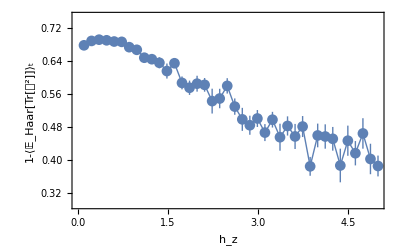

```mathematica
fig=ListPlot[data,
PlotRange->{All,{0.29,0.75}},
Joined->True,PlotMarkers->Automatic,
PlotStyle->Directive[Thin,FontSize->20],
Frame->True,FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{TraditionalForm[Subscript[h, z]],TraditionalForm[1-"⟨𝔼_Haar[Tr[𝒟^2]]⟩_t"]}
]
```

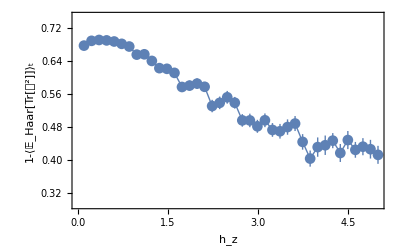

```mathematica
fig=ListPlot[data,
PlotRange->{All,{0.29,0.75}},
Joined->True,PlotMarkers->Automatic,
PlotStyle->Directive[Thin,FontSize->20],
Frame->True,FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{TraditionalForm[Subscript[h, z]],TraditionalForm[1-"⟨𝔼_Haar[Tr[𝒟^2]]⟩_t"]}
]
```

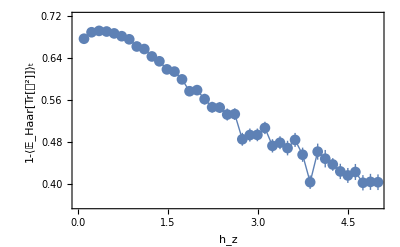

```mathematica
fig=ListPlot[data,
PlotRange->{All,{0.36,0.72}},
Joined->True,PlotMarkers->Automatic,
PlotStyle->Directive[Thin,FontSize->20],
Frame->True,FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{TraditionalForm[Subscript[h, z]],TraditionalForm[1-"⟨𝔼_Haar[Tr[𝒟^2]]⟩_t"]}
]
```

```mathematica
filename="figs_ja/temporal_avg_haar_avg_choi_purity/xxx_w_noise_L_"<>ToString[L]<>"_hx_1.pdf";
Export[filename,fig,"PDF",ImageResolution->300]
```

figs_ja/temporal_avg_haar_avg_choi_purity/xxx_w_noise_L_7_hx_1.pdf

```mathematica
RunProcess[{"pdfcrop",filename,filename}]
```

<|ExitCode→0,StandardOutput→PDFCROP 1.42, 2023/04/15 - Copyright (c) 2002-2023 by Heiko Oberdiek, Oberdiek Package Support Group.
==> 1 page written on `figs_ja/temporal_avg_haar_avg_choi_purity/xxx_w_noise_L_7_hx_1.pdf'.
,StandardError→|>

### Comparación r y pureza de Choi

```mathematica
hz=Subdivide[0.05,4.96,29];
r=Flatten[Import["~/Documents/chaos_meets_channels/ja_files/data/mean_level_spacing_ratio/rs_mat_L_12_px_30_Heis.csv","Table"]];
r=If[#<0.386,0.386,If[#>0.531,0.531,#]]&/@r;
r=Rescale[r,MinMax[r]];
r=Table[{hz[[i]],r[[i]]},{i,30}];
```

```mathematica
data=Transpose[{data[[All,1]],Rescale[#,MinMax[#]]&[data[[All,2]]]}]
```

{{0.1,0.950.15},{0.225641,0.990.15},{0.351282,1},{0.476923,1.000.15},{0.602564,0.980.15},{0.728205,0.960.15},{0.853846,0.940.15},{0.979487,0.900.14},{1.10513,0.880.14},{1.23077,0.830.14},{1.35641,0.800.14},{1.48205,0.750.14},{1.60769,0.730.14},{1.73333,0.680.14},{1.85897,0.600.14},{1.98462,0.610.14},{2.11026,0.550.13},{2.2359,0.500.13},{2.36154,0.500.13},{2.48718,0.450.13},{2.61282,0.450.13},{2.73846,0.290.13},{2.8641,0.310.13},{2.98974,0.320.13},{3.11538,0.360.13},{3.24103,0.240.13},{3.36667,0.260.13},{3.49231,0.230.13},{3.61795,0.280.13},{3.74359,0.180.13},{3.86923,0.000.12},{3.99487,0.200.13},{4.12051,0.160.13},{4.24615,0.120.12},{4.37179,0.070.12},{4.49744,0.050.12},{4.62308,0.070.12},{4.74872,0},{4.87436,0.000.12},{5.,0.000.12}}

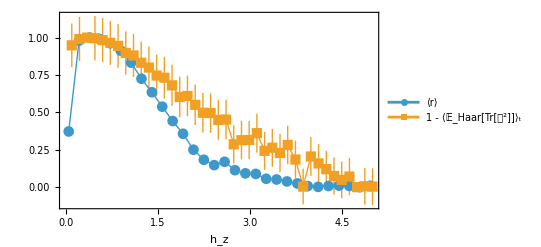

```mathematica
fig=ListPlot[{r,data},
PlotRange->All,
Joined->True,PlotMarkers->Automatic,
PlotStyle->Directive[Thin,FontSize->20],
Frame->True,FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{TraditionalForm[Subscript[h, z]]},
PlotLegends->Placed[{"⟨r⟩","1 - ⟨𝔼_Haar[Tr[𝒟^2]]⟩_t"},{Right,0.82}],
LabelStyle->Directive[Black,FontSize->16]
]
```

```mathematica
filename="~/Documents/chaos_meets_channels/ja_files/figs_ja/temporal_avg_haar_avg_choi_purity/heisenberg_L_7.pdf";
Export[filename,fig,"PDF",ImageResolution->300];RunProcess[{"pdfcrop",filename,filename}];
```